# Report Project 1

Course code: IX1500
Date: 2017-09-13

Evan Saboo, name1@kth.se
Xing Guan, xguan@kth.se

Task 1a: Poker Probability by census method

## Summery

### Task

The first task is to calculate the exact probability of the following hands in a variation of a poker game:

one pair

two pairs

three of a kind

four of a kind

five of a kind

full hand

straight

flush

straight flush

nothing

To calculate the exact probability  we will be using the census method.
The poker game consists of the cards 8,9,10,J,Q,K,A from two decks to construct sets of five playing cards. If one of the hand does contain more than one rank then the highest rank is considered e.g. if we want to calculate the probability of three of a kind and one of hands contains one pair, two pairs, three of a kind and full hand then the highest rank (full hand) is considered and it will be excluded from the calculation.

### Result

We have below constructed a table which shows the probability for each poker rank, from the lowest to the highest rank.

Hand | Probability | Probability,%
One pair | 11920/22737 | 52.426
Two pair | 870/7579 | 11.479
Three of a kind | 2240/22737 | 9.852
Four of a kind | 140/22737 | 0.616
Five of a kind | 7/68211 | 0.01
Full hand | 392/22737 | 1,724
Straight | 1360/53053 | 2.563
Flush | 953/477477 | 0.200
Straight flush | 16/159159 | 0.01
Nothing | 1360/7579 | 0,179

## Calculating poker Probability by census method

First we construct the 5 cards 8,9,10,J,Q,K,A with their respective colors. Every card has 4 distinct colors (Red,  Black, Green, Blue), which means that we have to separate by distinct numbers. This is the the result we get for one deck:

{{108,109,110,111,112,113,114},
{208,209,210,211,212,213,214},
{308,309,310,311,312,313,314},
{408,409,410,411,412,413,414}}

We represent the hundreds digit as the color and the two last numbers as the card, e.g. the card 108 has the color Red and has the card value 8 while the card 208 has the same card value but not the same color.

We construct another identical deck and join it with the first deck to get a every value we need from the two deck in one set:

{108,108,109,109,110,110,111,111,112,112,113,113,114,114,
208,208,209,209,210,210,211,211,212,212,213,213,214,214,
308,308,309,309,310,310,311,311,312,312,313,313,314,314,
408,408,409,409,410,410,411,411,412,412,413,413,414,414}

We also sorted the set in numerical order to calculate the probability for each rank without adding extra condition to each calculation.

The last step is to generate all possible hands with five card in each hand:

{{108,108,109,109,110},
{108,108,109,109,110},
«3819813»,
{412,413,413,414,414}}
 
 The total possible hands we can get is 3819816.

### One pair

To calculate the probability for the first and lowest rank one pair, we used a function to sum up all generated hands which contains one pair. We excluded all the colors from every card to check if two card values are identical. *
We also excluded all the hands which contains; two pairs, three of a kind and flush, because we want to filter out every rank higher than one pair. 
The total amount of hands which contains only contains one pair is 2 002 560.
By dividing the total number of hands which contains one pair with the total possible hands we get the exact probability of getting one pair:

11920/22737= 52.426%

### Two pairs

The total amount of hands which contains only contains one pair is 2 002 560.
By dividing the total number of hands which contains one pair with the total possible hands we get the exact probability of getting one pair:

11920/22737= 52.426%

## Code

```mathematica
deck1 = Range[8,14];
deck = Table[deck1, {4}];
For[i=1,i<Length[deck]+1,i++, deck[[i]] = deck[[i]] + i*100   ];
deck= Sort[Join[deck[[1]], deck[[1]],deck[[2]],deck[[2]],deck[[3]],deck[[3]], deck[[4]], deck[[4]]]] ;

(*This is 2 set of decks ranging from 8 to A*)
hands = Subsets[deck, {5}];
```

```mathematica
(*straight flush*)
Clear[straightFlush];
straightFlush[h_]:=h-h[[1]]=={0,1,2,3,4};
amountStraightFlush  = Count[hands, _? (straightFlush)] / Length[hands]
```

16/159159

```mathematica
Clear[flush]
flush[h_] := Equal@@ Quotient[h,100];
countFlush = (((Count[hands, _? (flush)])/ Length[hands]) -amountStraightFlush)
```

953/477477

```mathematica
(*straight*)
Clear[straight];
straight[h_] :=  MatchQ[h-h[[1]],{0,1,2,3,4}];
straights[v_] := straight[Sort[Mod[v,100]]];
((Count[hands, _? (straights)])/ Length[hands]) -amountStraightFlush
```

1360/53053

```mathematica
(*Full house*)
Clear[fullHand]
fullHand[{x_,x_,x_,y_, y_}/; x≠y]:= True; 
fullHand[{x_,x_,y_,y_, y_}/; x≠y]:= True; (*five of a kind*)
fullHand[_]:=False ; (* else *)
fullHands[h_] := fullHand[Sort[Mod[h,100]]]; 
Count[hands, _? (fullHands)] / Length[hands]
```

392/22737

```mathematica
(*Five of a kind*)
Clear[fiveKind]
fiveKind[{x_,x_,x_,x_, x_}]:= True; (*five of a kind*)
fiveKind[_]:=False ; (* else *)
fiveKinds[h_] := fiveKind[Sort[Mod[h,100]]]; 
Count[hands, _? (fiveKinds)] / Length[hands]
```

7/68211

```mathematica
(*Four of a kind*)
Clear[fourKind]
fourKind[{x_,x_,x_,x_, x_}]:= False;
fourKind[{___,x_,x_,x_,x_,___}]:=True; 
fourKind[_]:=False ; (* else *)
fourKinds[h_] := fourKind[Sort[Mod[h,100]]]; 
Count[hands, _? (fourKinds)] / Length[hands]
```

140/22737

```mathematica
(*three of a kind*)
Clear[threeKindQ];
threeKindQ[{___,x_,x_,x_,x_,___}]:=False; (* four of a kind *)
threeKindQ[{x_,x_,x_,y_,y_}/; x ≠ y] := False;
threeKindQ[{x_,x_,y_,y_,y_}/; x ≠ y] := False;
threeKindQ[{___,x_,x_,x_,___}]:=True; (* three of a kind *)
threeKindQ[{___}]:=False ; (* else *)
threeKindQs[h_] := threeKindQ[Sort[Mod[h,100]]]; 
(Count[hands, _? (threeKindQs)])/ Length[hands]
```

2240/22737

```mathematica
(*Two pairs*)
Clear[twoPairQ]
twoPairQ[{___,x_,x_,x_, ___}]:=False;
twoPairQ[{___,x_,x_,y_,y_,___}/;x≠y]:=True; 
twoPairQ[{___}]:=False ; (* else *)
twoPairQs[h_] := twoPairQ[Sort[Mod[h,100]]]&&(!flush[h]); 
(Count[hands, _? (twoPairQs)])/ Length[hands]
```

870/7579

```mathematica
(*one pair*)
Clear[pairQ]
pairQ[{___,x_,x_,___,y_,y_,___}/;x≠y]:=False; (* two pairs *)
pairQ[{___,x_,x_,x_, ___}]:=False;(* three of a kind *)
pairQ[{___,x_,x_,___}]:=True; (* a pair *)
pairQ[{___}]:=False ; (* else *)
pairQs[h_] := pairQ[Sort[Mod[h,100]]] &&(!flush[h]);
(Count[hands, _? (pairQs)])/ Length[hands]
```

11920/22737

```mathematica
Clear[nothing]
nothing[{___,x_,x_,___}]:=False;
nothing[{___}]:=True ;(* else *)
nothings[h_] := nothing[Sort[Mod[h,100]]]&&(!flush[h])&&(!straight[h])
(Count[hands, _? (nothings)])/ 
Length[hands]
```

1360/7579

Task 1b: Poker Probability by combinatorial calculus

## Summery

### Task

The second task is to use combinatorial calculus to calculate the probability of flush, straight, full house, 3 of a kind and 4 of a kind. Every rank has to be compared to task 1a to check if the answers match.

### Result

The differential equations are solved numerically for different angles and then a function L(θ) is interpolated whose maximum is determined.

L_max≈35m, θ_max≈42°

Hand | Probability | Probability,%
Flush | □ | □
Straight | □ | □
Full house | □ | □
Three of a kind | □ | □

## Kick Length

### Solution to the differential equations

The angle θ is set which gives initial values (x(0),y(0))=(0,0) och (x'(0),y'(0))=v_0(cos(θ),sin(θ)). Thereafter, the differential equations are solved numerically.

{m x''(t)=-μ x'(t)√((x'(t))^2)
m y''(t)=-m g-μ y'(t)√((y'(t))^2)

The kick time t_0 is determined so that y(t_0)=0. Finally, the kick length is L=x(t_0).

The above procedure is repeated for different angles and then interpolated a function L(θ) whose maximum is determined.

L_max≈35m, θ_max≈42°

### Calculation of kick time and kick length

The time t_0 is determined so that y(t_0)=0. Finally the kick length is computed as L=x(t_0).

The solution is repeated for different angles and then interpolated a function L(θ) whose maximum is determined.

θ | 10 | 20 | 30 | 40 | 50 | 60 | 70 | 80
L | 17.2434 | 27.3526 | 32.7388 | 34.6327 | 33.6694 | 30.0809 | 23.7545 | 14.1591

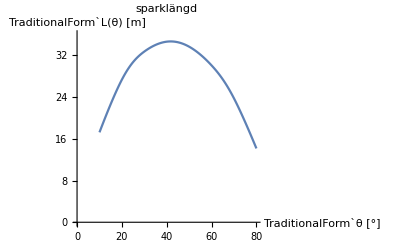

The maximum is computed as

L_max≈35m, θ_max≈41°

## Code

Task 1c: Poker Probability by Monte Carlo method

## Summery

### Task

In the last task we are going to calculate the probability of getting one pair using the Monte Carlo method. We will also draw a diagram that shows how the probability estimate stabilises with increasing sample size. This task will also be compared to task 1a to check if our approximate answer is close to the exact answer.

### Result

The differential equations are solved numerically for different angles and then a function L(θ) is interpolated whose maximum is determined.

L_max≈35m, θ_max≈42°

## Kick Length

### Solution to the differential equations

The angle θ is set which gives initial values (x(0),y(0))=(0,0) och (x'(0),y'(0))=v_0(cos(θ),sin(θ)). Thereafter, the differential equations are solved numerically.

{m x''(t)=-μ x'(t)√((x'(t))^2)
m y''(t)=-m g-μ y'(t)√((y'(t))^2)

The kick time t_0 is determined so that y(t_0)=0. Finally, the kick length is L=x(t_0).

The above procedure is repeated for different angles and then interpolated a function L(θ) whose maximum is determined.

L_max≈35m, θ_max≈42°

### Calculation of kick time and kick length

The time t_0 is determined so that y(t_0)=0. Finally the kick length is computed as L=x(t_0).

The solution is repeated for different angles and then interpolated a function L(θ) whose maximum is determined.

θ | 10 | 20 | 30 | 40 | 50 | 60 | 70 | 80
L | 17.2434 | 27.3526 | 32.7388 | 34.6327 | 33.6694 | 30.0809 | 23.7545 | 14.1591

-Graphics-

The maximum is computed as

L_max≈35m, θ_max≈41°

## Code

Enter given data.

```mathematica
m=0.4;μ=0.01;g=9.8;v0=25;
```

Define differential equations and there initial conditions.

```mathematica
de[θ_]:={
m x''[t]==-μ x'[t] √(x'[t]^2),
m y''[t]==-m g-μ y'[t] √(y'[t]^2),
x[0]==0,y[0]==0,x'[0]==v0 Cos[θ],y'[0]==v0 Sin[θ]
}
```

Solve the DE.

```mathematica
sol[θ_]:=NDSolve[de[θ],{x,y},{t,0,5}]
```

Example for θ=45°

```mathematica
sol[45°]
```

{{x→InterpolatingFunction[{{0., 5.}}, <>],y→InterpolatingFunction[{{0., 5.}}, <>]}}

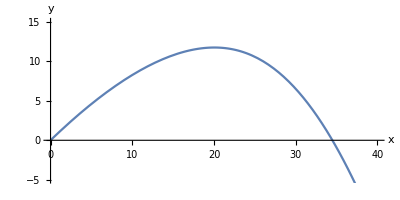

```mathematica
ParametricPlot[
Evaluate[{x[t],y[t]}/.sol[45°]],{t,0,3.5},
AxesLabel->{"x","y"},PlotRange->{{0,40},{-5,15}}
]
```

The curve for different angles.

```mathematica
Manipulate[
ParametricPlot[
Evaluate[{x[t],y[t]}/.sol[θ]],{t,0,3.5},
AxesLabel->{"x","y"},
PlotLabel->StringForm["θ = `1`°",θ/Degree],
PlotRange->{{0,40},{-5,15}}
],
{{θ,45°},25°,55°}
]
```

ReplaceAll::reps: {sol[45 °]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {sol[0.785398]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

The function for kick length.

```mathematica
len[θ_]:=Module[
{t0},
t0=t/.FindRoot[Evaluate[y[t]/.sol[θ]]==0,{t,2,4}];
First[x[t0]/.sol[θ]]
]
```

Example

```mathematica
len[45°]
```

34.4855

A table for different angles.

```mathematica
data=Table[{θ,len[θ °]},{θ,10,80,10}]
```

{{10,17.2434},{20,27.3526},{30,32.7388},{40,34.6327},{50,33.6694},{60,30.0809},{70,23.7545},{80,14.1591}}

```mathematica
TableForm[Transpose[data],TableHeadings->{{θ,L},None}]
```

θ | 10 | 20 | 30 | 40 | 50 | 60 | 70 | 80
L | 17.2434 | 27.3526 | 32.7388 | 34.6327 | 33.6694 | 30.0809 | 23.7545 | 14.1591

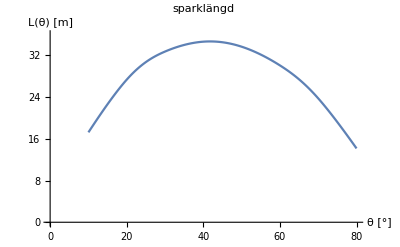

```mathematica
ListLinePlot[data,InterpolationOrder->3,PlotRange->{0,36},AxesLabel->{StringForm["`1` [°]",θ],StringForm["`1` [m]",L[θ]]},PlotLabel->"sparklängd"]
```

Higher accuracy around the max value.

```mathematica
data2=Table[{θ Degree,len[θ Degree]},{θ,35,45,1}]
```

{{35 °,34.0717},{36 °,34.2433},{37 °,34.3846},{38 °,34.4963},{39 °,34.5789},{40 °,34.6327},{41 °,34.6584},{42 °,34.6561},{43 °,34.6264},{44 °,34.5694},{45 °,34.4855}}

Now, search for the maximum.

```mathematica
max=FindMaximum[length[θ],{θ,40°,45°}]
```

FindMaximum::nrnum: The function value -length[0.698132] is not a real number at {θ} = {0.698132}.

FindMaximum[length[θ],{θ,40 °,45 °}]

```mathematica
θ0=(θ/.max⟦2⟧)/Degree
```

FindMaximum::nrnum: The function value -length[0.698132] is not a real number at {θ} = {0.698132}.

ReplaceAll::reps: {θ,40 °,45 °} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

(θ/.{θ,40 °,45 °})/°